# FAQ : SSS Dimension

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

Visually, SSS networks can be identified as 1-dimensional, 2-dimensional, etc. Ex/

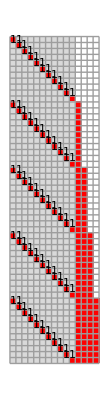



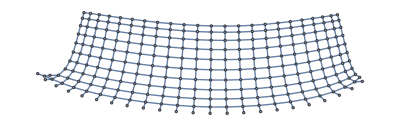
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss3,Min->1,Max->255,SSSMin->Automatic,SSSMax->55,NetMin->Automatic,NetMax->Automatic,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot},ImageSize->287.,NetSize->{Automatic,300},SSSSize->{Automatic,288.},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False]
```

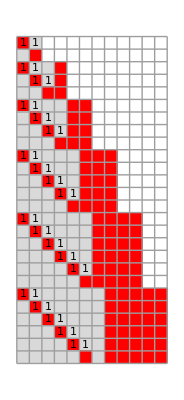
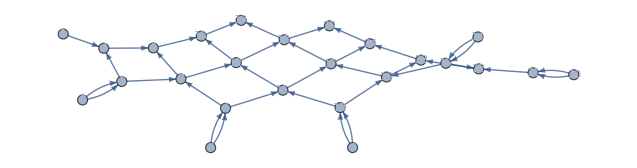
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSS[{"BA"->"AB",""->"BA"},"BA",25];
```

But we want the program to identify the dimension automatically, by considering the patterns of the node numbers.

1. Start with a list of event/node indices, either from the SSS or from the network. These should be special in some way.
2. Create a table of nth-differences from the list. If row k is constant, the dimension of the original data is k.

Example:

Original arbitrary data, which we can immediately identify as a list of squares: 1 4 9 16 25 36 49

Tables of differences

1 4 9 16 25 36 49

3 5 7 9 11 13

2 2 2 2 2

We call the initial data row 0, the first row of differences is row 1, etc. Since the first constant row is row 2, this data should be identified as 2-dimensional, which agrees with the exponent of 2 (squares) in the formula for the data: y = x^2. Similarly, forming a table of differences starting with data generated by any polynomial formula, y = cx^2+ ..., will end up with a constant n-th row.

No row in the difference table of an exponential network ever becomes constant (nor even a straight line), just as repeated derivatives of exponential functions are all exponentials, never constant. To identify them we take ratios of neighboring elements in the rows of the difference table. If any row of this ratio table becomes an integer constant, all further rows will also be constant, and exponential behavior is demonstrated. The constant found is the average out-degree of nodes of the network -- the number of graph branches leading out from the nodes.

Problems:

1. Initial irregularities before the pattern sets in. How to decide how much to ignore?

2. Fractional dimension in the difference table: no row is exactly constant, but the slope of the best fit lines changes from positive to negative, and then the values begin to fluctuate ever more wildly. The point where this happens approximates the dimension, but somehow we need to be able to calculate the fractional part.

3. Fractional exponential dimension: if, for example, half the nodes have out-degree 2 and half have 3, the average is 2.5, and the constant should be 2.5, but in fact the rows don't exactly become 2.5, only close, and then start to fluctuate again.

Possible solutions:

1. Ignore first 10% of the data to try to get past initial irregularities. If irregularities persist, try further evolution: in theory, the irregular portion will eventually be included in the 10%.

2. Try summing pairs, triples, etc., in the data and difference rows, to smooth out fluctuations.

3. Fit the initial data row to y = cx^n and to y = cn^x, and see which gives the best fit (R-squared value closest to 1). Problem: not a straight line due to additional terms in the formula.

4. Fit to each row of the differences table in turn until we get an R-squared value that is better than the following row. The fit should keep getting better as additional polynomial terms disappear with successive differences.

5. (If using a network: Turn the network (with edges of the form n -> m) into a list of sets of edge/link lengths, as we have been doing.) But then rather than simply taking repeated differences of adjacent terms or terms having some fixed separation (the triangular patterns above), at each "level" form the n^th differences for terms separated by 0, 1, 2, …, terms. So rather than an upside down triangle, we'll have an upside down tetrahedron, with each level being a triangle. If at some row m of some level n we come to a lot of 0 entries, that was a productive choice for m and n: the pattern is revealed by subtracting terms separated by m neighbors, a constant row reached after n - 1 differences, a 0 row after n differences, indicating dimension n - 1. 
.

## Ambiguous Dimension

An exciting and not well understood development is that sometimes the dimensionality tests give differing results.

First type:  either 2-d or exponential

DistanceTally considers the network to be two-dimensional, but all other tests (and a visual inspection) call it exponential.  There is severe delay in completing one side of the network, and apparent bunching on the other, but plotting all nodes a distance n from the origin does result in a flat network.

(insert example here)

Second type:  either 2-d or 1-d

DistanceTally reports 1-d, others 2-d.  Example:  403701: {“AB”->”BA”, “”->”AB”} : 1x2

The problem here is that only nodes 1, 4, 8, 13, 19, 26, 34, 43, 53, …, can be reached from the origin (node 1), so all other nodes are by definition ∞ steps away.

In[266]:= $SSSDistance

Out[266]= {0, ∞, ∞, 1, ∞, ∞, ∞, 2, ∞, ∞, ∞, ∞, 3, ∞, ∞, ∞, ∞, ∞, 4, ∞, ∞, ∞, ∞, ∞, ∞, 5, ∞, ∞, ∞, ∞, ∞, ∞, ∞, 6, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, 7, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, 8, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, ∞, 9}

Should we revise the definition of dimension to treat all links in the causal network as bidirectional, for the purposes of “distance from origin”?  But the direction of the arrows is the local direction of time flow, so this really is a case of “you can’t get there from here”.    But of course other tests say 2-d, since the network can be contained in the plane but not on a line without bunching up nodes.

Thoughts, anyone?

Lucas has emailed some thoughts, some of which definitely apply here, others we may decide to move to different pages:

Prof. Caviness has previously discussed time in the causal network template within two contexts: 
-          Microtime :: :: enumeration sequence
-          Macrotime :: :: network model

Original depiction. Pending upload.
Tentative illustration (requires revision). See attached.

[Note: Microtime is indicated here by the network edges (links), with the direction of time flow always going from the smaller number to the larger number. Two alternative macrotimes (observer-dependent) are shown by the unprimed and prime (purple and yellow) clumping.  The only restriction on the position of the macrotime divisions is that no arrows may go backwards, from “later” to “earlier” times, and thus causality is still guaranteed. It is interesting that in special relativity causality is also preserved. --kc]

Einstein forced physics to consider the observer. Lorentz’s math redefined the perception of simultaneity. Time dilation is observable for speeds at or exceeding (0.1) c; so is a linear treatment of time necessarily appropriate? All physical order seems reducible to the simple harmonic oscillator archetype, such as, ex. the valence superposition of electrons in molecular bonding. Time inherently confers a quality of periodicity, so can we treat time as a harmonic oscillator with an equilibrium position that can be stretched within limits of the maximum wave amplitude? In context to the node-of-origin inaccessibility proposed by Prof. Caviness – can the margins of the amplitude, if exceeded, correlate to an authentic past and unattainable temporal frame of reference, as opposed to a spatial constraint?

In regard to application of n-dimensionality ‘tests’: can tests be applied to localized segments of a network or are tests always run on the entire network? This is where my knowledge deficit is most evident.. The algorithms are formulated based on the (linear?) enumeration sequence to manipulate node-encoding components, but not necessarily in consideration of the structural orientation of the causal network model, which is deferred to visual inspection?

The discrepant ambiguity in dimensionality analysis test results are condensed to either, (1) operator experimental error (programming conflict) or, to infer upon the motives of Caviness introjecting this inquiry, (2) there exists inherent dimensionality-uncertainty in the physical nature of the network – credit to Heisenberg.

Regarding causal network mechanics, should the connectivity fabric be treated as a static, immobile entity or does the network stretch, bend, vibrate, fold, or hold properties of elasticity and malleability? Something will eventually perturb the network state, maybe? The configuration of nodes and connectivity of events conferring the fundamental enumeration schemes can remain constant while experiencing conformational transformations (analogous to oscillating about an equilibrium position, or cyclohexane transitions between conformer states), correct? How else can macrotime-dependent causal violations be avoided – or is it solely the orientation plane of the observer that changes?

What is the nature of the conflict proposed by Prof. Caviness? The concept of network-origin inaccessibility to certain nodes: is the premise of ‘permitted conditions’ or ‘violation of causality’ appropriate? Is this what is meant by “you can’t get there from here”? Is this equivalent to “that has already happened, you can’t experience that anymore”? Is the spatial inaccessibility of certain nodes to the site-of-origin purely a matter of linear conflict?

If infinite-distance (inaccessible) nodes relative to the origin have imposed their ruleset-determined changes in a past-macrotime, and as the origin inertial frame observer is not necessarily bothered by simultaneous events, what significance is there to inquire upon spatial incongruity of the network vector space? The thought requires attention to dimensional homogeneity within the network architecture, as such, is the network required to maintain constant dimensional character throughout its corporeal entirety? What if focal (network) segments retain unique dimensional features while cumulatively contributing – ultimately – to the downstream dimensional manifold destined by ruleset enumeration? High node-densities in the reduced dimensional plane correspond to distinctive facets of an incomplete or dysmorphic network, or perhaps a network that has yet to reveal its existential essence, and, if in fact, therein involves a kinetic destiny, could the motion correct the dimensional incongruity?
Is the node density on a two-dimensional plane representative of the tensor character in a three-dimensional coordinate axis?

Further, Prof. Caviness has discussed ‘edge’-effects, or unique localized nodal distributions partial to network boundaries. Edges are reasonably synonymous with surfaces, and surfaces innately hold some degree of curvature (a straight mirror nonetheless is thought to be a convex surface), so do the dimensionality tests require modification if evaluating a surface-edge region? Do network boundaries have spatial privileges, such as to access the nodes that seem illogically out of reach to our frame of reference?

“Drew wondered whether there could be a closed loop in a network.  Preliminary answer:  No, since the causal arrows always point toward higher-numbered nodes.”

This exact question I have struggled with as well. Can the network not collapse into itself or shift its growth trajectory back towards the origin which can interfere with previously arranged network components? Can the network introduce “creation” events upon a voxel of which the territory is saturated by former node occupancy?

Random:

(Invalid/rhetorical) Is frequency, or the oscillatory properties of the fundamental quantum fields, the absolute invariance in the physical world? 
Can dimensionality be defined in terms of a frequency parameter?
Are there rulesets that impose node-character exchanges on two separate segments of the string within a single event-node?

Thank you for any time spent reading these words.
-lv